```mathematica
dataA={{1,248},{2,262},{3,372},{4,526},{5,742},{6,958},{7,1215},{8,1471},{9,1738},{10,1936},{11,1971},{12,2147},{13,2258},{14,2418},{15,2567},{16,2688},{17,2809},{18,2925},{19,3026},{20,3205},{21,3348},{22,3476},{23,3573},{24,3719},{25,3750},{26,3952},{27,4048},{28,4137},{29,4251},{30,4301},{31,4351},{32,4401},{33,4439},{34,4488},{35,4548},{36,4596},{37,4629},{38,4680},{39,4713},{40,4749},{41,4783},{42,4817},{43,4849},{44,4877},{45,4901},{46,4928},{47,4950},{48,4970},{49,4998},{50,5024},{51,5060},{52,5085},{53,5088},{54,5090},{55,5110},{56,5129},{57,5139},{58,5167},{59,5186}}
```

{{1,248},{2,262},{3,372},{4,526},{5,742},{6,958},{7,1215},{8,1471},{9,1738},{10,1936},{11,1971},{12,2147},{13,2258},{14,2418},{15,2567},{16,2688},{17,2809},{18,2925},{19,3026},{20,3205},{21,3348},{22,3476},{23,3573},{24,3719},{25,3750},{26,3952},{27,4048},{28,4137},{29,4251},{30,4301},{31,4351},{32,4401},{33,4439},{34,4488},{35,4548},{36,4596},{37,4629},{38,4680},{39,4713},{40,4749},{41,4783},{42,4817},{43,4849},{44,4877},{45,4901},{46,4928},{47,4950},{48,4970},{49,4998},{50,5024},{51,5060},{52,5085},{53,5088},{54,5090},{55,5110},{56,5129},{57,5139},{58,5167},{59,5186}}

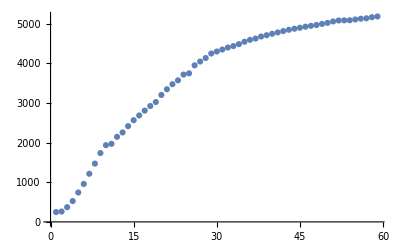

```mathematica
ListPlot[dataA]
```

```mathematica
ShortGoel=a*(1-Exp[-b*t]);
GeneralGoel=a*(1-Exp[-b*t^c]);
delayedSshapedModel=a (1-(1+b*t) Exp[-b*t]);
shortGoel = NonlinearModelFit[dataA,ShortGoel,{a,b},t]
```

FittedModel[5878.82 (1-ⅇ^(-«19» t))]

```mathematica
shortGoel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 5878.82 | 79.9984 | 73.4867 | 3.65502×10^-58
b | 0.0399199 | 0.00120955 | 33.0039 | 7.68528×10^-39

```mathematica
/** Параметрите са значими 
-standard error< estimate &
- t-Statistic >2 &
p-Value<0.05/
```

```mathematica
shortGoel["BestFitParameters"]
```

{a→5878.82,b→0.0399199}

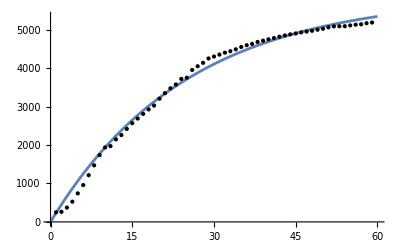

```mathematica
Plot[shortGoel[t],{t,0,60},Epilog->Point[dataA]]
```

```mathematica
shortGoel["AIC"]
```

749.911

```mathematica
shortGoel["BIC"]
```

756.144

```mathematica
shortGoel["RSquared"]
```

0.998873

```mathematica
shortGoel["AdjustedRSquared"]
```

0.998833

```mathematica
generalGoel=NonlinearModelFit[dataA,GeneralGoel,{{a,5190},b,c},t]
```

FittedModel[5284.65 (1-ⅇ^(-«21» t^(«19»)))]

```mathematica
generalGoel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 5284.65 | 29.8211 | 177.212 | 1.09216×10^-78
b | 0.0223466 | 0.000981266 | 22.7732 | 5.41985×10^-30
c | 1.25716 | 0.0170309 | 73.8166 | 1.72321×10^-57

```mathematica
/** Параметрите са значими 
-standard error< estimate &
- t-Statistic >2 &
p-Value<0.05/
```

```mathematica
generalGoel["BestFitParameters"]
```

{a→5284.65,b→0.0223466,c→1.25716}

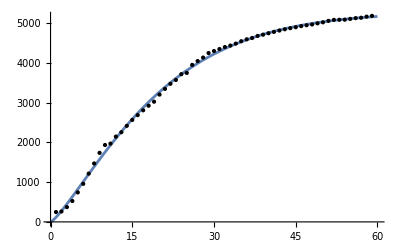

```mathematica
Plot[generalGoel[t],{t,0,60},Epilog->Point[dataA]]
```

```mathematica
delayed = NonlinearModelFit[dataA,delayedSshapedModel,{a,b},t]
```

FittedModel[5103.37 (1-ⅇ^(-«20» t) (1+0.111952 t))]

```mathematica
delayed["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 5103.37 | 34.2725 | 148.906 | 1.50431×10^-75
b | 0.111952 | 0.00172427 | 64.9268 | 3.91684×10^-55

```mathematica
/** Параметрите са значими 
-standard error< estimate &
- t-Statistic >2 &
p-Value<0.05/
```

```mathematica
delayed["BestFitParameters"]
```

{a→5103.37,b→0.111952}

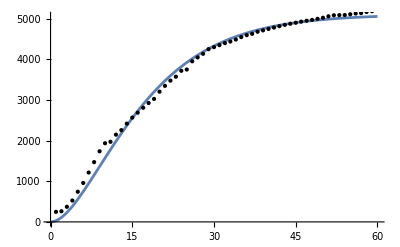

```mathematica
Plot[delayed[t],{t,0,60},Epilog->Point[dataA]]
```

```mathematica
Gompertz=a*Exp[-α*Exp[-β*t]]
gompertz=NonlinearModelFit[dataA,Gompertz,{{a,5185},{α,0.3},{β,0.1}},t]
```

a ⅇ^(-ⅇ^(-t β) α)

FittedModel[5167.93 ⅇ^(-2.78272 «1»)]

```mathematica
gompertz["Function"]
```

5167.93 ⅇ^(-2.78272 ⅇ^(-0.0899422 #1))&

```mathematica
gompertz["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 5167.93 | 29.8527 | 173.114 | 4.03853×10^-78
α | 2.78272 | 0.0693337 | 40.1351 | 5.88018×10^-43
β | 0.0899422 | 0.0019979 | 45.0184 | 1.14706×10^-45

```mathematica
/** Параметрите са значими 
-standard error< estimate &
- t-Statistic >2 &
p-Value<0.05/
```

```mathematica
gompertz["BestFitParameters"]
```

{a→5167.93,α→2.78272,β→0.0899422}

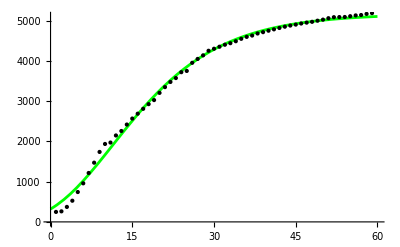

```mathematica
Plot[gompertz[t],{t,0,60},Epilog-> Point[dataA],PlotStyle-> Green]
```

```mathematica
GompertzMakeham=a*(1-Exp[-λ*t-(α/β)*(Exp[β*t]-1)]);
gm=NonlinearModelFit[dataA,GompertzMakeham,{{a,5200},α,λ,{β,0.1}},t]
```

FittedModel[5316.18 (1-ⅇ^(-«19» (-1+«1»)-«1»))]

```mathematica
gm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 5316.18 | 56.0196 | 94.8987 | 1.17222×10^-62
α | -0.0426225 | 0.00672701 | -6.33603 | 4.58768×10^-8
λ | 0.0695012 | 0.00864887 | 8.03587 | 7.62333×10^-11
β | -0.077343 | 0.0296347 | -2.60988 | 0.0116457

```mathematica
/** α ,β са незначими параметри за модела/
```

```mathematica
gm["BestFitParameters"]
```

{a→5316.18,α→-0.0426225,λ→0.0695012,β→-0.077343}

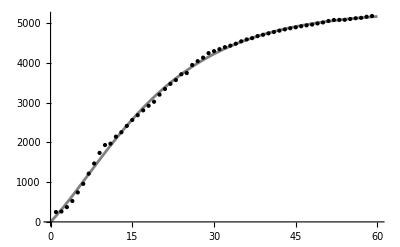

```mathematica
Plot[gm[t],{t,0,60},Epilog-> Point[dataA],PlotStyle->Gray]
```

```mathematica
Grid[{#,shortGoel[#],generalGoel[#],delayed[#],gompertz[#],gm[#]}&[{"AIC","BIC","RSquared","AdjustedRSquared"}],Frame->All]
```

AIC | BIC | RSquared | AdjustedRSquared
749.911 | 756.144 | 0.998873 | 0.998833
652.624 | 660.934 | 0.999791 | 0.999779
748.173 | 754.406 | 0.998905 | 0.998867
709.218 | 717.528 | 0.999454 | 0.999424
658.075 | 668.463 | 0.999778 | 0.999762

```mathematica
/** Най- ниски резултати за AIC и BIC получаваме при General Goel . Резултатите за RSquared и AdjustedRSquared са най- близки до 1 при General Goel -> най- добрият модел е General Goel. (Следващият най- добър е Gompertz Makeham.)/
```

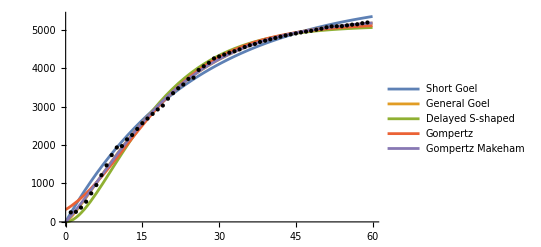

```mathematica
Plot[{shortGoel[t],generalGoel[t],delayed[t],gompertz[t],gm[t]},{t,0,60},PlotLegends->{"Short Goel","General Goel", "Delayed S-shaped","Gompertz","Gompertz Makeham"},PlotStyle->{"red","green","blue","pink","yellow"}, Epilog->Point[dataA]]
```

```mathematica
prediction = Table[{i,Round[generalGoel[i]]},{i,60,150}]
```

{{60,5171},{61,5180},{62,5188},{63,5196},{64,5203},{65,5209},{66,5215},{67,5221},{68,5226},{69,5230},{70,5235},{71,5239},{72,5243},{73,5246},{74,5249},{75,5252},{76,5255},{77,5257},{78,5259},{79,5261},{80,5263},{81,5265},{82,5267},{83,5268},{84,5270},{85,5271},{86,5272},{87,5273},{88,5274},{89,5275},{90,5276},{91,5277},{92,5277},{93,5278},{94,5279},{95,5279},{96,5280},{97,5280},{98,5280},{99,5281},{100,5281},{101,5281},{102,5282},{103,5282},{104,5282},{105,5282},{106,5283},{107,5283},{108,5283},{109,5283},{110,5283},{111,5283},{112,5283},{113,5284},{114,5284},{115,5284},{116,5284},{117,5284},{118,5284},{119,5284},{120,5284},{121,5284},{122,5284},{123,5284},{124,5284},{125,5284},{126,5284},{127,5284},{128,5284},{129,5284},{130,5284},{131,5284},{132,5284},{133,5284},{134,5285},{135,5285},{136,5285},{137,5285},{138,5285},{139,5285},{140,5285},{141,5285},{142,5285},{143,5285},{144,5285},{145,5285},{146,5285},{147,5285},{148,5285},{149,5285},{150,5285}}

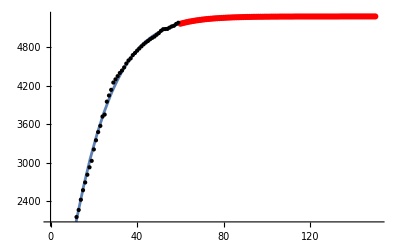

```mathematica
Show[Plot[generalGoel[t],{t,0,151},Epilog-> Point[dataA]],ListPlot[prediction,PlotStyle->Red]]
```